```mathematica
Convolve[SquareWave[2Pi*100*t],HeavisideTheta[t],t,x]
```

Convolve[SquareWave[200 π t],HeavisideTheta[t],t,x]

```mathematica
Plot[Convolve[SquareWave[2Pi*100*t],HeavisideTheta[t],t,x],{x,0,0.04}]
```

```mathematica
Convolve[1000*Exp[-1000*t],HeavisideTheta[t],t,x]
```

-ⅇ^(-1000 x)

```mathematica
Convolve[1000*Exp[-1000*t],DiracDelta[t],t,x]
```

1000 ⅇ^(-1000 x)

```mathematica
DiscreteConvolve[1000*Exp[-1000*n],DiscreteDelta[n],n,m]
```

1000 ⅇ^(-1000 m)

```mathematica
Convolve[1000*Exp[-1000*t],DiracComb[100*t],t,x]
```

```mathematica
DiscreteConvolve[1000*Exp[-1000*n],DiscreteDelta[n]+DiscreteDelta[n+0.01]+DiscreteDelta[n+0.02]+DiscreteDelta[n+0.03],n,m]
```

1000 (ⅇ^(-1000 m)+DiscreteConvolve[ⅇ^(-1000 n),DiscreteDelta[0.01+n],n,m]+DiscreteConvolve[ⅇ^(-1000 n),DiscreteDelta[0.02+n],n,m]+DiscreteConvolve[ⅇ^(-1000 n),DiscreteDelta[0.03+n],n,m])

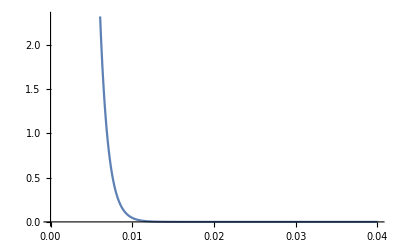

```mathematica
Plot[1000 ⅇ^(-1000 t),{t,0,0.04}]
```